```mathematica
traindata=ExampleData[{"MachineLearning","MNIST"},"TrainingData"];
```

```mathematica
mtestset=ExampleData[{"MachineLearning","MNIST"},"TestData"];
```

```mathematica
indexs=Table[i,{i,1,Length[traindata]}];
indexs=RandomSample[indexs];
mvalidset=traindata[[indexs[[1;;10000]]]];
mtrainset=traindata[[indexs[[10001;;60000]]]];
```

```mathematica
mtrainset[[1,1]]
```

-Graphics-

Classificateur de Bayes:
On entraîne le classificateur sur l’ensemble d’entraînement et on évalue la performance sur l’ensemble mtrainset, mtestset.

```mathematica
c=Classify[mtrainset,Method->"NaiveBayes"]
```

ClassifierFunction[…]

```mathematica
ClassifierInformation[c]
```

Classifier information
Input type | Image
Number of classes | 10
Method | NaiveBayes
Accuracy | 84.4 % ± 1.2 %
Loss | 4.17 ± 0.48
Evaluation time | 340. µs/example
Classifier memory | 3.94 MB
Training examples used | 50000 examples
Training time | 1 5
 |

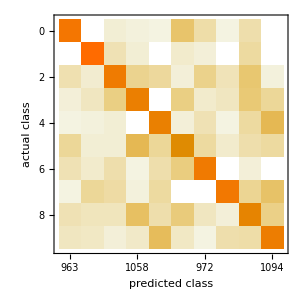
{0.1528,-Graphics-}

```mathematica
ClassifierMeasurements[c, mtestset,{"Error","ConfusionMatrixPlot"}]
```

```mathematica
ClassifierMeasurements[c, mtestset,{"LogLikelihood","ConfusionMatrixPlot"}]
```

{-46631.8,-Graphics-}

```mathematica
ClassifierMeasurements[c, mtestset,{"MeanCrossEntropy","ConfusionMatrixPlot"}]
```

{4.66318,-Graphics-}

On cherche l’hyper-paramètre optimal SmoothingParameter sur l’ensemble de validation mvalidset.  On entraîne le classificateur sur l’ensemble d’entraînement et on évalue le performance sur l’ensemble mtrainset, mvalidset.

```mathematica
{c2,c3,c4,c5,c6}=Classify[mtrainset, Method->{"NaiveBayes","SmoothingParameter"->#}]&/@{.2,.5,2,20,40};
```

training error:

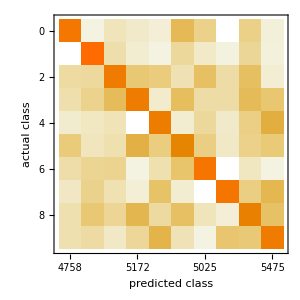
{0.155,-Graphics-}

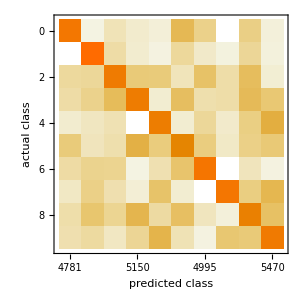
{0.15456,-Graphics-}

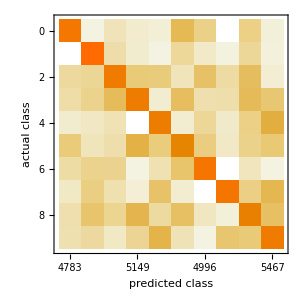
{0.15492,-Graphics-}

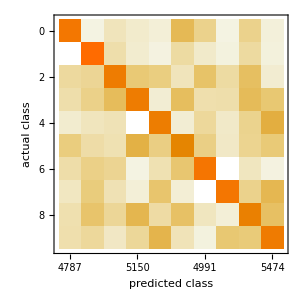
{0.15656,-Graphics-}

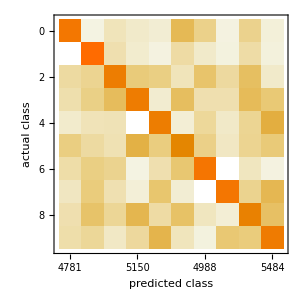
{0.15794,-Graphics-}

```mathematica
Print ["training error:"]
ClassifierMeasurements[c2, mtrainset,{"Error","ConfusionMatrixPlot"}]
ClassifierMeasurements[c3, mtrainset,{"Error","ConfusionMatrixPlot"}]
ClassifierMeasurements[c4, mtrainset,{"Error","ConfusionMatrixPlot"}]
ClassifierMeasurements[c5, mtrainset,{"Error","ConfusionMatrixPlot"}]
ClassifierMeasurements[c6, mtrainset,{"Error","ConfusionMatrixPlot"}]
```

validation error:

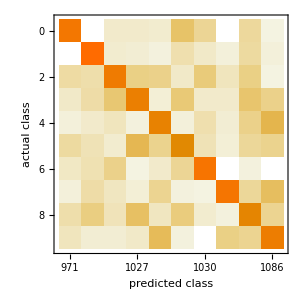
{0.1673,-Graphics-}

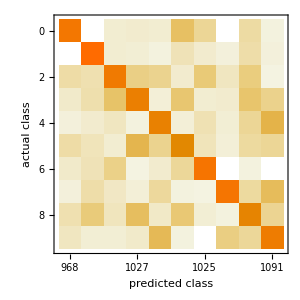
{0.1642,-Graphics-}

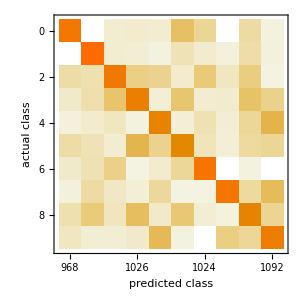
{0.1646,-Graphics-}

{0.1658}

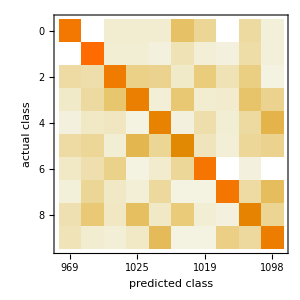
{0.1668,-Graphics-}

```mathematica
Print ["validation error:"]
ClassifierMeasurements[c2, mvalidset,{"Error","ConfusionMatrixPlot"}]
ClassifierMeasurements[c3, mvalidset,{"Error","ConfusionMatrixPlot"}]
ClassifierMeasurements[c4, mvalidset,{"Error","ConfusionMatrixPlot"}]
ClassifierMeasurements[c5, mvalidset,{"Error"}]
ClassifierMeasurements[c6, mvalidset,{"Error","ConfusionMatrixPlot"}]
```

Résumé: l’erreur de validation augmente et l’erreur d’entraînement aussi augmente. 
Donc, le SmoothingParameter optimal est .5, on évalue la performance sur l’ensemble de test.

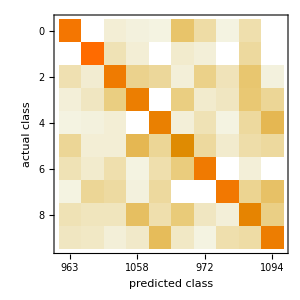
{0.1529,-Graphics-}

```mathematica
ClassifierMeasurements[c3, mtestset,{"Error","ConfusionMatrixPlot"}]
```

Bien Classifié et Mal Classifié

```mathematica
ClassifierMeasurements[c3, mtestset,{"BestClassifiedExamples"}]
ClassifierMeasurements[c3, mtestset,{"WorstClassifiedExamples"}]
```

{{-Graphics-→0,-Graphics-→0,-Graphics-→6,-Graphics-→0,-Graphics-→0,-Graphics-→0,-Graphics-→0,-Graphics-→0,-Graphics-→0,-Graphics-→0}}

{{-Graphics-→1,-Graphics-→2,-Graphics-→2,-Graphics-→1,-Graphics-→7,-Graphics-→2,-Graphics-→3,-Graphics-→6,-Graphics-→9,-Graphics-→1}}

```mathematica
SupportVectorMachine Classifieur:
```

On entraîne le classificateur sur l’ensemble d’entraînement et évalue la performance sur l’ensemble mtrainset, mtestset.

```mathematica
c1=Classify[mtrainset,Method->{"SupportVectorMachine", "KernelType"->"Linear"}]
```

ClassifierFunction[…]

```mathematica
ClassifierInformation[c1]
```

Classifier information
Input type | Image
Number of classes | 10
Method | SupportVectorMachine
Accuracy | 92.9 % ± 0.17 %
Loss | 0.326 ± 0.01
Evaluation time | 335. µs/example
Classifier memory | 135. MB
Training examples used | 50000 examples
Training time | 18 55
 |

```mathematica
c2=Classify[mtrainset,Method->{"SupportVectorMachine", "KernelType"->"RadialBasisFunction"}]
```

ClassifierFunction[…]

```mathematica
ClassifierInformation[c2]
```

Classifier information
Input type | Image
Number of classes | 10
Method | SupportVectorMachine
Accuracy | 90.1 % ± 0.72 %
Loss | 0.327 ± 0.027
Evaluation time | 853. µs/example
Classifier memory | 222. MB
Training examples used | 50000 examples
Training time | 34 46
 |

```mathematica
c3=Classify[mtrainset,Method->{"SupportVectorMachine", "KernelType"->"Polynomial"}]
```

ClassifierFunction[…]

```mathematica
ClassifierInformation[c3]
```

Classifier information
Input type | Image
Number of classes | 10
Method | SupportVectorMachine
Accuracy | 95.7 % ± 0.2 %
Loss | 0.218 ± 0.013
Evaluation time | 686. µs/example
Classifier memory | 118. MB
Training examples used | 50000 examples
Training time | 17 7
 |

On évalue la performance sur l’ensemble mtrainset, mtestset.

training error:

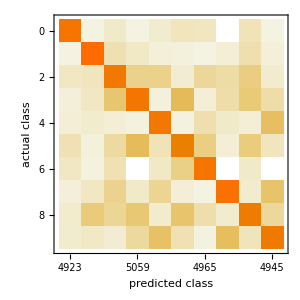
{0.03832,-Graphics-}

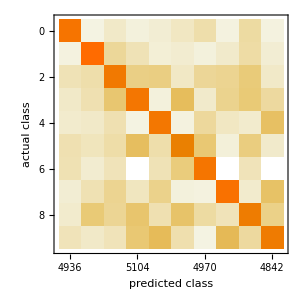
{0.04654,-Graphics-}

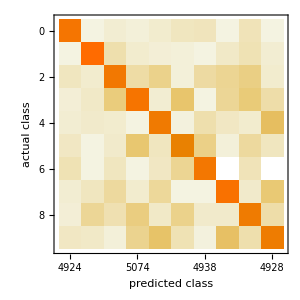
{0.02696,-Graphics-}

```mathematica
Print["training error:"]
ClassifierMeasurements[c1, mtrainset,{"Error","ConfusionMatrixPlot"}]
ClassifierMeasurements[c2, mtrainset,{"Error","ConfusionMatrixPlot"}]
ClassifierMeasurements[c3, mtrainset,{"Error","ConfusionMatrixPlot"}]
```

test error:

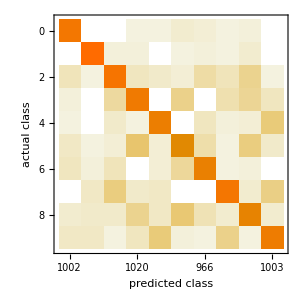
{0.0524,-Graphics-}

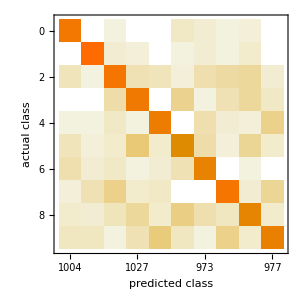
{0.0493,-Graphics-}

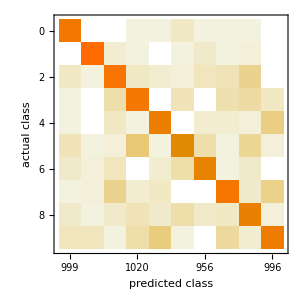
{0.0372,-Graphics-}

```mathematica
Print["test error:"]
ClassifierMeasurements[c1, mtestset,{"Error","ConfusionMatrixPlot"}]
ClassifierMeasurements[c2, mtestset,{"Error","ConfusionMatrixPlot"}]
ClassifierMeasurements[c3, mtestset,{"Error","ConfusionMatrixPlot"}]
```

Donc, l’erreur de test diminue. Le noyau de type polynomial est le meilleur classificateur. On va chercher l’hyper-paramètre optimal sur l’ensemble validation.
On entraîne le classificateur pour PolynomialDegree 3,4,5,9

```mathematica
{c4,c5,c6,c7}=Classify[mtrainset, Method->{"SupportVectorMachine", "KernelType"->"Polynomial","PolynomialDegree"->#}]&/@{3,4,5,9};
```

$Aborted

On évalue la performance sur l’ensemble de validation.

```mathematica
Print["validation error:"]
ClassifierMeasurements[c4, mvalidset,{"Error","ConfusionMatrixPlot"}]
ClassifierMeasurements[c5, mvalidset,{"Error","ConfusionMatrixPlot"}]
ClassifierMeasurements[c6, mvalidset,{"Error","ConfusionMatrixPlot"}]
ClassifierMeasurements[c7, mvalidset,{"Error","ConfusionMatrixPlot"}]
```

validation error:

{0.0397}

{0.0314}

{0.0257}

{0.0234}

Donc, l’erreur de validation diminue. Le degré 9 est la meilleure valeur pour l’hyper-paramètre. On va chercher le GammaScalingParameter optimal sur l’ensemble validation.

On entraîne le classificateur pour GammaScalingParameter .0001

```mathematica
c8=Classify[mtrainset, Method->{"SupportVectorMachine", "KernelType"->"Polynomial","PolynomialDegree"->9, "GammaScalingParameter"-> 0.0001}]
```

ClassifierFunction[…]

On entraîne le classificateur pour GammaScalingParameter .001

```mathematica
c9=Classify[mtrainset, Method->{"SupportVectorMachine", "KernelType"->"Polynomial","PolynomialDegree"->9, "GammaScalingParameter"-> 0.001}]
```

ClassifierFunction[…]

On entraîne le classificateur pour GammaScalingParameter .01

```mathematica
c10=Classify[mtrainset, Method->{"SupportVectorMachine", "KernelType"->"Polynomial","PolynomialDegree"->9, "GammaScalingParameter"-> 0.01}]
```

ClassifierFunction[…]

On entraîne le classificateur pour GammaScalingParameter .1

```mathematica
c11=Classify[mtrainset, Method->{"SupportVectorMachine", "KernelType"->"Polynomial","PolynomialDegree"->9, "GammaScalingParameter"-> 0.1}]
```

ClassifierFunction[…]

On entraîne le classificateur pour GammaScalingParameter 1

```mathematica
c12=Classify[mtrainset, Method->{"SupportVectorMachine", "KernelType"->"Polynomial","PolynomialDegree"->9, "GammaScalingParameter"-> 1}]
```

ClassifierFunction[…]

On entraîne le classificateur pour GammaScalingParameter 10

```mathematica
c13=Classify[mtrainset, Method->{"SupportVectorMachine", "KernelType"->"Polynomial","PolynomialDegree"->9, "GammaScalingParameter"-> 10}]
```

ClassifierFunction[…]

```mathematica
Print["validation error:"]
ClassifierMeasurements[c8, mvalidset,{"Error","ConfusionMatrixPlot"}]
ClassifierMeasurements[c9, mvalidset,{"Error","ConfusionMatrixPlot"}]
ClassifierMeasurements[c10, mvalidset,{"Error","ConfusionMatrixPlot"}]
ClassifierMeasurements[c11, mvalidset,{"Error","ConfusionMatrixPlot"}]
ClassifierMeasurements[c12, mvalidset,{"Error","ConfusionMatrixPlot"}]
ClassifierMeasurements[c13, mvalidset,{"Error","ConfusionMatrixPlot"}]
```

validation error:

{0.0578}

{0.0223}

{0.0183}

{0.0184}

{0.018}

{0.018}

L’erreur de validation diminue pour Gamma 1.  Donc, le Gamma optimal est 1.
On évalue la performance sur l’ensemble de test.

test error:

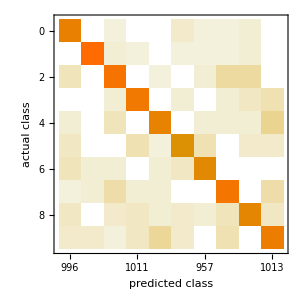
{0.0197,-Graphics-}

```mathematica
Print["test error:"]
ClassifierMeasurements[c12, mtestset,{"Error","ConfusionMatrixPlot"}]
```

Bien classifié et mal classifié

```mathematica
ClassifierMeasurements[c12, mtestset,{"BestClassifiedExamples"}]
ClassifierMeasurements[c12, mtestset,{"WorstClassifiedExamples"}]
```

{{-Graphics-→3,-Graphics-→3,-Graphics-→3,-Graphics-→3,-Graphics-→0,-Graphics-→4,-Graphics-→3,-Graphics-→3,-Graphics-→3,-Graphics-→3}}

{{-Graphics-→6,-Graphics-→7,-Graphics-→1,-Graphics-→1,-Graphics-→3,-Graphics-→9,-Graphics-→6,-Graphics-→9,-Graphics-→5,-Graphics-→0}}

ClassMeanCrossEntropy

```mathematica
ClassifierMeasurements[c12, mtestset,{"ClassMeanCrossEntropy"}]
```

{<|0→0.0481591,1→0.0412797,2→0.102197,3→0.0769102,4→0.0698301,5→0.102043,6→0.105144,7→0.0975343,8→0.106559,9→0.130516|>}

```mathematica
Remove[traindata]
```

```mathematica
(* CIFAR-10 *)
obj=ResourceObject["CIFAR-10"]
```

ResourceObject[…]

```mathematica
traindata=ResourceData[obj,"TrainingData"];
ctestset=ResourceData[obj,"TestData"];
indexs=Table[i,{i,1,Length[traindata]}];
indexs=RandomSample[indexs];
cvalidset = traindata[[indexs[[1;;2000]]]];
ctrainset = traindata[[indexs[[2001;;12000]]]];
```

```mathematica
data2 = ColorConvert[Table[cvalidset[[i,1]],{i,1,2000}],"Grayscale"];
data3= ColorConvert[Table[ctrainset[[i,1]],{i,1,10000}],"Grayscale"];
```

```mathematica
data4=ColorConvert[Table[ctestset[[i,1]],{i,1,10000}],"Grayscale"];
```

```mathematica
cvalidset =Table[data2[[i]]->cvalidset[[i,2]],{i,1,2000}];
```

```mathematica
ctrainset = Table[data3[[i]]->ctrainset[[i,2]],{i,1,10000}];
```

```mathematica
ctestset= Table[data4[[i]]->ctestset[[i,2]],{i,1,10000}];
```

Classificateur de Bayes naïf:
On entraîne le classificateur sur l’ensemble d’entraînement et on évalue la performance sur l’ensemble ctrainset, ctestset.

```mathematica
c=Classify[ctrainset,Method->"NaiveBayes"]
```

ClassifierFunction[…]

```mathematica
ClassifierInformation[c]
```

Classifier information
Input type | Image
Number of classes | 10
Method | NaiveBayes
Accuracy | 26.1 % ± 0.98 %
Loss | 100. ± 2.8
Evaluation time | 140. µs/example
Classifier memory | 16.8 MB
Training examples used | 10000 examples
Training time | 31.5 s
 |

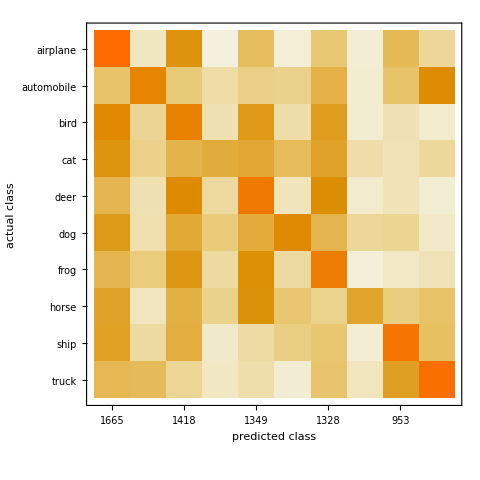
{0.7363,-Graphics-}

```mathematica
ClassifierMeasurements[c, ctestset,{"Error","ConfusionMatrixPlot"}]
```

On cherche l’hyper-paramètre SmoothingParameter optimal sur l’ensemble de validation cvalidset.  On entraîne le classifieur sur l’ensemble d’entraînement et on évalue la performance sur l’ensemble ctrainset, cvalidset.

```mathematica
{c2,c3,c4,c5,c6}=Classify[ctrainset, Method->{"NaiveBayes","SmoothingParameter"->#}]&/@{.2,.5,2,20,40};
```

training error:

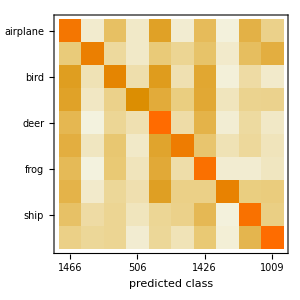
{0.5879,-Graphics-}

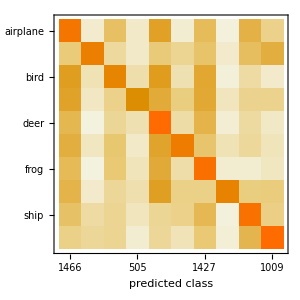
{0.5881,-Graphics-}

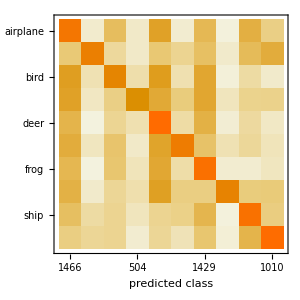
{0.5882,-Graphics-}

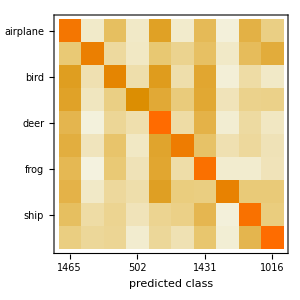
{0.5884,-Graphics-}

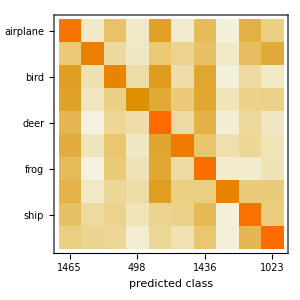
{0.5893,-Graphics-}

validation error:

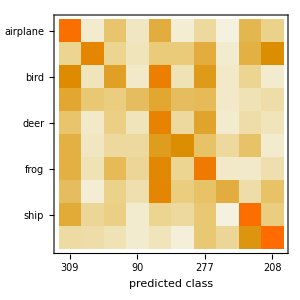
{0.7385,-Graphics-}

{0.7385,-Graphics-}

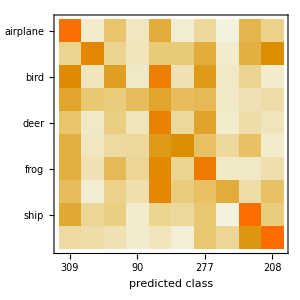
{0.7385,-Graphics-}

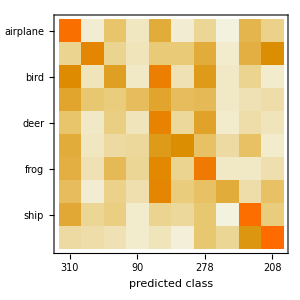
{0.7385,-Graphics-}

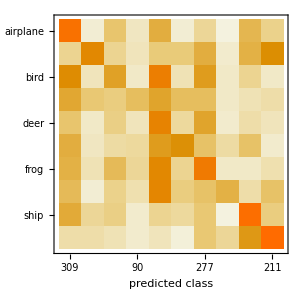
{0.739,-Graphics-}

```mathematica
Print ["training error:"]
ClassifierMeasurements[c2, ctrainset,{"Error","ConfusionMatrixPlot"}]
ClassifierMeasurements[c3, ctrainset,{"Error","ConfusionMatrixPlot"}]
ClassifierMeasurements[c4, ctrainset,{"Error","ConfusionMatrixPlot"}]
ClassifierMeasurements[c5, ctrainset,{"Error","ConfusionMatrixPlot"}]
ClassifierMeasurements[c6, ctrainset,{"Error","ConfusionMatrixPlot"}]

Print ["validation error:"]
ClassifierMeasurements[c2, cvalidset,{"Error","ConfusionMatrixPlot"}]
ClassifierMeasurements[c3, cvalidset,{"Error","ConfusionMatrixPlot"}]
ClassifierMeasurements[c4, cvalidset,{"Error","ConfusionMatrixPlot"}]
ClassifierMeasurements[c5, cvalidset,{"Error","ConfusionMatrixPlot"}]
ClassifierMeasurements[c6, cvalidset,{"Error","ConfusionMatrixPlot"}]
```

Résumé: l’erreur de validation augmente et l’erreur d’entraînement aussi augmente. 
Donc, le SmoothingParameter optimal est .2, on évalue le performance sur ensemble de test.

```mathematica
ClassifierMeasurements[c2, ctestset,{"Error","ConfusionMatrixPlot"}]
```

{0.7363,-Graphics-}

Bien Classifié et Mal Classifié

```mathematica
Print["Bien Classifier"]
ClassifierMeasurements[c2, ctestset,{"BestClassifiedExamples"}]
Print["Mal Classifier"]
ClassifierMeasurements[c2, ctestset,{"WorstClassifiedExamples"}]
```

Bien Classifier

{{-Graphics-→airplane,-Graphics-→airplane,-Graphics-→airplane,-Graphics-→airplane,-Graphics-→airplane,-Graphics-→airplane,-Graphics-→airplane,-Graphics-→airplane,-Graphics-→airplane,-Graphics-→airplane}}

Mal Classifier

{{-Graphics-→deer,-Graphics-→frog,-Graphics-→frog,-Graphics-→airplane,-Graphics-→bird,-Graphics-→airplane,-Graphics-→airplane,-Graphics-→airplane,-Graphics-→airplane,-Graphics-→airplane}}

Class MeanCrossEntropy

```mathematica
ClassifierMeasurements[c2, ctestset,{"ClassMeanCrossEntropy"}]
```

{<|airplane→107.819,automobile→84.8275,bird→136.234,cat→114.467,deer→92.229,dog→103.251,frog→104.181,horse→100.049,ship→94.4154,truck→74.3134|>}

SupportVectorMachine Classifieur:
On entraîne le classifieur sur l’ensemble d’entraînement et on évalue la performance sur l’ensemble ctrainset, ctestset.

```mathematica
c2=Classify[ctrainset,Method->{"SupportVectorMachine", "KernelType"->"Linear"}]
```

ClassifierFunction[…]

```mathematica
ClassifierInformation[c2]
```

Classifier information
Input type | Image
Number of classes | 10
Method | SupportVectorMachine
Accuracy | 9.66 % ± 0.4 %
Loss | 2.67 ± 0.015
Evaluation time | 169. µs/example
Classifier memory | 434. MB
Training examples used | 10000 examples
Training time | 12 12
 |

```mathematica
c3=Classify[ctrainset,Method->{"SupportVectorMachine", "KernelType"->"RadialBasisFunction"}]
```

ClassifierFunction[…]

```mathematica
ClassifierInformation[c3]
```

Classifier information
Input type | Image
Number of classes | 10
Method | SupportVectorMachine
Accuracy | 9.94 % ± 1.1 %
Loss | 2.35 ± 0.014
Evaluation time | 568. µs/example
Classifier memory | 717. MB
Training examples used | 10000 examples
Training time | 18 48
 |

```mathematica
c4=Classify[ctrainset,Method->{"SupportVectorMachine", "KernelType"->"Polynomial"}]
```

ClassifierFunction[…]

On évalue la performance sur l’ensemble ctrainset, ctestset.

```mathematica
Print["training error:"]
ClassifierMeasurements[c2, ctrainset,{"Error","ConfusionMatrixPlot"}]
ClassifierMeasurements[c3, ctrainset,{"Error","ConfusionMatrixPlot"}]
ClassifierMeasurements[c4, ctrainset,{"Error","ConfusionMatrixPlot"}]

Print["test error:"]
ClassifierMeasurements[c2, ctestset,{"Error","ConfusionMatrixPlot"}]
ClassifierMeasurements[c3, ctestset,{"Error","ConfusionMatrixPlot"}]
ClassifierMeasurements[c4, ctestset,{"Error","ConfusionMatrixPlot"}]
```

training error:

{0.5469}

{0.8272}

{0.7524}

test error:

{0.782}

{0.8213}

{0.7502}

Donc, l’erreur de test diminue. Le noyau de type polynomial est le meilleur classificateur. On va chercher l’hyper-paramètre optimal sur l’ensemble validation.
On entraîne le classificateur pour PolynomialDegree 3,4,5,9

```mathematica
{c5,c6,c7,c8}=Classify[ctrainset, Method->{"SupportVectorMachine", "KernelType"->"Polynomial","PolynomialDegree"->#}]&/@{3,4,5,9};
```

On évalue la performance sur l’ensemble de validation.

```mathematica
Print["validation error:"]
ClassifierMeasurements[c5, cvalidset,{"Error","ConfusionMatrixPlot"}]
ClassifierMeasurements[c6, cvalidset,{"Error","ConfusionMatrixPlot"}]
ClassifierMeasurements[c7, cvalidset,{"Error","ConfusionMatrixPlot"}]
ClassifierMeasurements[c8, cvalidset,{"Error","ConfusionMatrixPlot"}]
```

validation error:

{0.75}

{0.845}

{0.7495}

{0.7375}

Donc, l’erreur de validation diminue. Le degré 9 est la meilleure valeur pour l’hyper-paramètre. On va chercher le GammaScalingParameter optimal sur l’ensemble validation.
On entraîne le classificateur pour GammaScalingParameter .0001

```mathematica
c13=Classify[ctrainset, Method->{"SupportVectorMachine", "KernelType"->"Polynomial","PolynomialDegree"->9, "GammaScalingParameter"-> 0.0001}]
```

ClassifierFunction[…]

On entraîne le classificateur pour GammaScalingParameter .001

```mathematica
c9=Classify[ctrainset, Method->{"SupportVectorMachine", "KernelType"->"Polynomial","PolynomialDegree"->9, "GammaScalingParameter"-> 0.001}]
```

ClassifierFunction[…]

On entraîne le classificateur pour GammaScalingParameter .01

```mathematica
c12=Classify[ctrainset, Method->{"SupportVectorMachine", "KernelType"->"Polynomial","PolynomialDegree"->9, "GammaScalingParameter"-> 0.01}]
```

ClassifierFunction[…]

On entraîne le classificateur pour GammaScalingParameter 1

```mathematica
c10=Classify[ctrainset, Method->{"SupportVectorMachine", "KernelType"->"Polynomial","PolynomialDegree"->9, "GammaScalingParameter"-> 1}]
```

ClassifierFunction[…]

On entraîne le classificateur pour GammaScalingParameter 10

```mathematica
c11=Classify[ctrainset, Method->{"SupportVectorMachine", "KernelType"->"Polynomial","PolynomialDegree"->9, "GammaScalingParameter"-> 10}]
```

ClassifierFunction[…]

```mathematica
Print["validation error:"]
ClassifierMeasurements[c13, cvalidset,{"Error","ConfusionMatrixPlot"}]
ClassifierMeasurements[c9, cvalidset,{"Error","ConfusionMatrixPlot"}]
ClassifierMeasurements[c12, cvalidset,{"Error","ConfusionMatrixPlot"}]
ClassifierMeasurements[c10, cvalidset,{"Error","ConfusionMatrixPlot"}]
ClassifierMeasurements[c11, cvalidset,{"Error","ConfusionMatrixPlot"}]
```

validation error:

{0.736}

{0.678}

{0.7155}

{0.776}

{0.7965}

L’erreur de validation diminue pour Gamma .001.  Donc, le Gamma optimal est .001.
On évalue la performance sur l’ensemble de test.

test error:

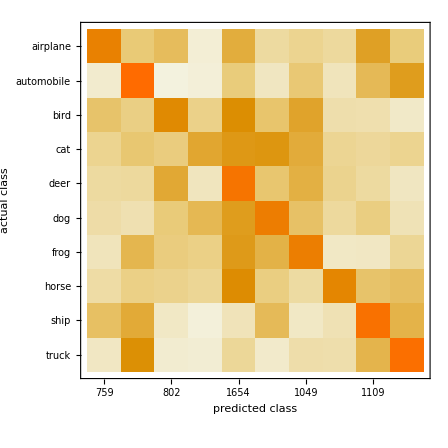
{0.6655,-Graphics-}

```mathematica
Print["test error:"]
ClassifierMeasurements[c9, ctestset,{"Error","ConfusionMatrixPlot"}]
```

Bien Classifié et Mal classifié

```mathematica
Print["Bien Classifier"]
ClassifierMeasurements[c9, ctestset,{"BestClassifiedExamples"}]
Print["Mal Classifier"]
ClassifierMeasurements[c9, ctestset,{"WorstClassifiedExamples"}]
```

Bien Classifier

{{-Graphics-→ship,-Graphics-→truck,-Graphics-→airplane,-Graphics-→airplane,-Graphics-→bird,-Graphics-→cat,-Graphics-→ship,-Graphics-→airplane,-Graphics-→airplane,-Graphics-→ship}}

Mal Classifier

{{-Graphics-→bird,-Graphics-→automobile,-Graphics-→truck,-Graphics-→truck,-Graphics-→truck,-Graphics-→frog,-Graphics-→truck,-Graphics-→ship,-Graphics-→bird,-Graphics-→truck}}

Class MeanCrossEntropy

```mathematica
ClassifierMeasurements[c9, ctestset,{"ClassMeanCrossEntropy"}]
```

{<|airplane→1.92674,automobile→1.90282,bird→2.03216,cat→2.15979,deer→2.44079,dog→2.06997,frog→2.23733,horse→2.00573,ship→2.05541,truck→1.88312|>}